```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zhan/Desktop/MacDesktop/fresco/1H4HE

```mathematica
Import["fort_MS_even.45","Table"];
MapAt[If[#<0,#+180,#] &,%,{All,2}];
MapAt[# 5/4 &,%,{All,1}];
Drop[%,None,{3,6}];
phaseMS=%;
```

```mathematica
Import["fort.45","Table"];
MapAt[If[#<0,#+180,#] &,%,{All,2}];
MapAt[# 5/4 &,%,{All,1}];
Drop[%,None,{3,6}];
phaseMSodd=%;
```

```mathematica
phaseSBB=Import["fort_SBB.45","Table"];
MapAt[If[#<0,#+180,#] &,%,{All,2}];
MapAt[# 5/4 &,%,{All,1}];
Drop[%,None,{3,6}];
phaseSBB=%;
```

## Import Experimental Data

```mathematica
sData=ImportString[" 8.4797E-01  1.6874E+02
 1.3859E+00  1.6383E+02
 1.8159E+00  1.5936E+02
 2.2464E+00  1.5578E+02
 2.6769E+00  1.5221E+02
 3.1071E+00  1.4819E+02
 4.5067E+00  1.3746E+02
 5.9085E+00  1.3075E+02
 7.8503E+00  1.2314E+02
 9.7929E+00  1.1687E+02
 1.1736E+01  1.1105E+02
 1.4002E+01  1.0344E+02
 1.7243E+01  9.9395E+01
 1.9835E+01  9.4460E+01
 2.4373E+01  8.9507E+01
 2.8263E+01  8.6793E+01
 3.0424E+01  8.4987E+01
 3.2153E+01  8.3632E+01
 3.4315E+01  8.2273E+01
 3.6908E+01  8.0017E+01
 3.9718E+01  7.8652E+01
","Table"];
```

```mathematica
dData15=ImportString[
"7.9120E+00  7.3283E-01
 1.0074E+01  1.4036E+00
 1.2069E+01  2.1805E+00
 1.4478E+01  3.3935E+00
 1.7633E+01  5.1541E+00
 2.0125E+01  6.4759E+00
 2.4684E+01  1.0194E+01
 2.8417E+01  1.2932E+01
 3.0740E+01  1.4468E+01
 3.2484E+01  1.5458E+01
 3.4561E+01  1.6343E+01
 3.7219E+01  1.7775E+01
 4.0039E+01  1.9856E+01
","Table"];
```

```mathematica
dData25=ImportString[
"9.9125E+00  6.4651E-01
 1.2075E+01  1.3173E+00
 1.4321E+01  1.9890E+00
 1.7563E+01  3.1031E+00
 2.0138E+01  4.4258E+00
 2.4627E+01  6.2007E+00
 2.8290E+01  6.7798E+00
 3.0535E+01  7.5594E+00
 3.2362E+01  8.4424E+00
 3.4523E+01  9.4369E+00
 3.7182E+01  1.0545E+01
 4.0090E+01  1.1979E+01",
"Table"];
pData05=ImportString[
"1.0290E+00  2.5966E-01
 1.5409E+00  2.2451E+00
 1.9645E+00  5.9615E+00
 2.3892E+00  8.9356E+00
 2.8135E+00  1.2157E+01
 3.3229E+00  1.5875E+01
 3.6625E+00  1.8353E+01
 5.1031E+00  3.0741E+01
 6.5445E+00  4.2635E+01
 8.5895E+00  5.2308E+01
 1.0725E+01  5.9014E+01
 1.2783E+01  5.9039E+01
 1.5015E+01  5.8323E+01
 1.8190E+01  5.7618E+01
 2.0509E+01  5.5419E+01
 2.4977E+01  5.0276E+01
 2.8412E+01  4.7596E+01
 3.0817E+01  4.6140E+01
 3.2706E+01  4.4678E+01
 3.4595E+01  4.3463E+01
","Table"];
pData15=ImportString["1.1088E+00  4.4668E+00
 1.6080E+00  1.5359E+01
 2.1837E+00  3.2686E+01
 2.8328E+00  5.8673E+01
 3.4000E+00  8.1937E+01
 3.8985E+00  9.3325E+01
 4.2310E+00  1.0075E+02
 5.7599E+00  1.1141E+02
 7.2164E+00  1.1266E+02
 9.1058E+00  1.1120E+02
 1.1083E+01  1.0826E+02
 1.3232E+01  1.0531E+02
 1.5383E+01  1.0064E+02
 1.8475E+01  9.7952E+01
 2.0798E+01  9.3526E+01
 2.5267E+01  8.7641E+01
 2.8791E+01  8.2982E+01
 3.1198E+01  7.9546E+01
 3.2831E+01  7.7339E+01
 3.4721E+01  7.5382E+01
","Table"];
```

## S wave phase shift

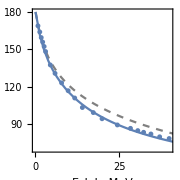

```mathematica
plotExpS05=ListPlot[sData,PlotMarkers->{Automatic, 5}];

Cases[phaseSBB,b__/;b⟦3⟧==0];
plotSBBS05=ListPlot[%⟦All,1;;2⟧,Joined->True,PlotStyle->{Gray,Dashed}];

Cases[phaseMS,b__/;b⟦3⟧==0];
plotMSS05=ListPlot[%⟦All,1;;2⟧,Joined->True];

plotS=Show[plotSBBS05, plotMSS05,plotExpS05,ImageSize->Small,PlotRange->{{0,40},{70,180}},FrameLabel->{"E_lab, MeV","δ, degree"},Frame->True,AspectRatio->1.0]
```

## P wave phase shift

```mathematica
plotExpP05=ListPlot[pData05,PlotMarkers->{"▲", 9}];
plotExpP15=ListPlot[pData15,PlotMarkers->{"▼", 9}];

Cases[phaseSBB,b__/;b⟦3⟧==1&&b⟦4⟧==0.5];
plotSBBP05=ListPlot[%⟦All,1;;2⟧,Joined->True,PlotStyle->{Gray,Dashed}];

Cases[phaseSBB,b__/;b⟦3⟧==1&&b⟦4⟧==1.5];
plotSBBP15=ListPlot[%⟦All,1;;2⟧,Joined->True,PlotStyle->{Gray,Dashed}];

Cases[phaseMSodd,b__/;b⟦3⟧==1&&b⟦4⟧==0.5];
plotMSP05=ListPlot[%⟦All,1;;2⟧,Joined->True];

Cases[phaseMSodd,b__/;b⟦3⟧==1&&b⟦4⟧==1.5];
plotMSP15=ListPlot[%⟦All,1;;2⟧,Joined->True];

plotP=Show[plotMSP05, plotMSP15,plotSBBP15,plotSBBP05,plotExpP15,plotExpP05,ImageSize->Small,PlotRange->{{0,40},{0,120}},FrameLabel->{"E_lab, MeV","δ, degree"},Frame->True,AspectRatio->1.0];
```

## D wave phase shift

```mathematica
plotExpD05=ListPlot[dData15,PlotMarkers->{"◆", 9}];
plotExpD15=ListPlot[dData25,PlotMarkers->{"◆", 9}];

Cases[phaseSBB,b__/;b⟦3⟧==2&&b⟦4⟧==1.5];
plotSBBD15=ListPlot[%⟦All,1;;2⟧,Joined->True,PlotStyle->{Gray,Dashed}];

Cases[phaseSBB,b__/;b⟦3⟧==2&&b⟦4⟧==2.5];
plotSBBD25=ListPlot[%⟦All,1;;2⟧,Joined->True,PlotStyle->{Gray,Dashed}];

Cases[phaseMS,b__/;b⟦3⟧==2&&b⟦4⟧==1.5];
plotMSD15=ListPlot[%⟦All,1;;2⟧,Joined->True];

Cases[phaseMS,b__/;b⟦3⟧==2&&b⟦4⟧==2.5];
plotMSD25=ListPlot[%⟦All,1;;2⟧,Joined->True];

plotD=Show[plotSBBD15, plotSBBD25,plotMSD15,plotMSD25,plotExpD05,plotExpD15,ImageSize->Small,PlotRange->{{0,40},{0,50}},FrameLabel->{"E_lab, MeV","δ, degree"},Frame->True,AspectRatio->1.0];
```

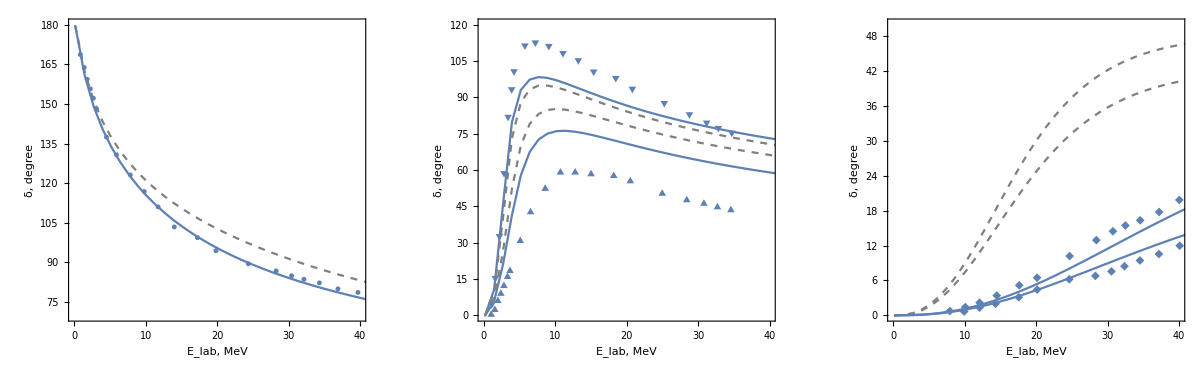

```mathematica
GraphicsRow[{plotS,plotP,plotD}]
```